(-1+x0) (-3+2 x0) (-x0^2+x1^2)-4 (-2 x0+x0^2+x1^2)^2

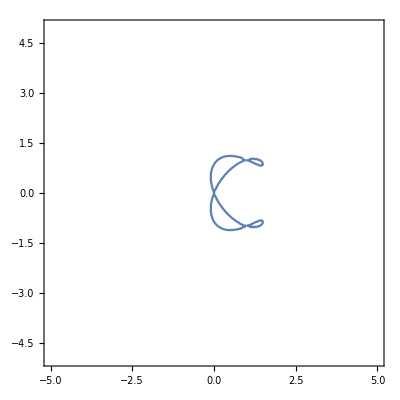

```mathematica
f = (x1^2 - x0^2)(x0 - 1)(2 x0 - 3) - 4(x0^2 + x1^2 - 2x0)^2
ContourPlot[f==0,{x0,-5,5},{x1,-5,5}]
```

38400+241920 u0+561664 u0^2+547456 u0^3+146272 u0^4-48048 u0^5+2736 u0^6-114672 u1^2-501344 u0 u1^2-726664 u0^2 u1^2-364472 u0^3 u1^2-35511 u0^4 u1^2+110776 u1^4+252776 u0 u1^4+120574 u0^2 u1^4-34295 u1^6

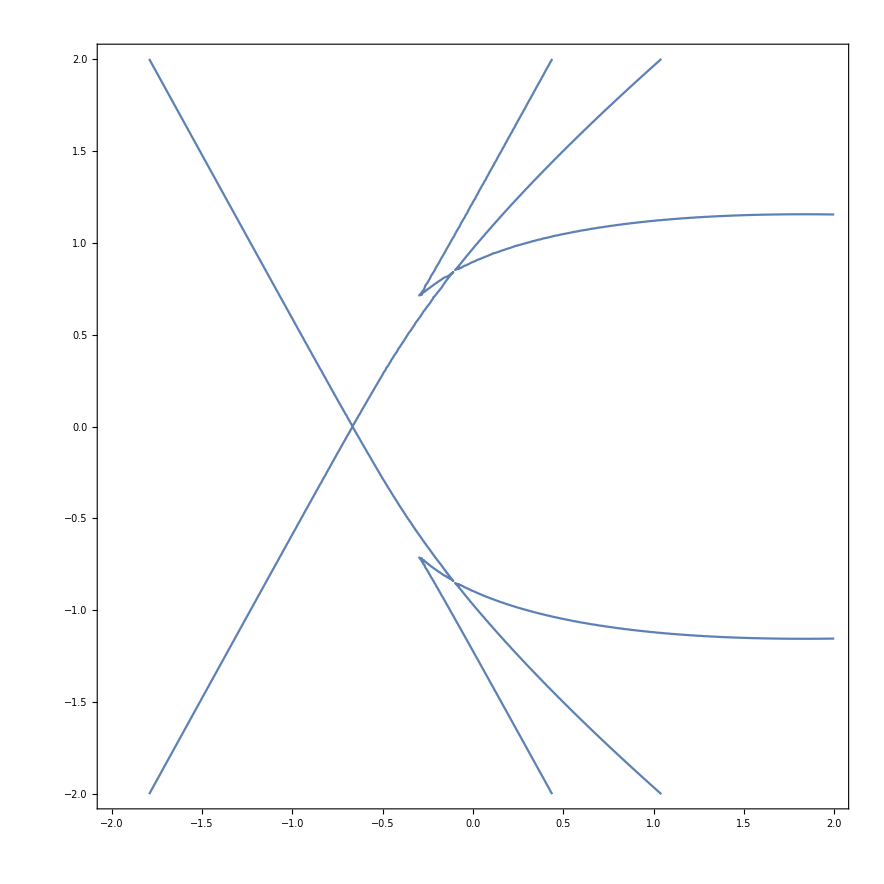

f

```mathematica
h = ResourceFunction["PolynomialHomogenize"][Expand[f],{x0, x1},x2];
h //InputForm

d = 2736*u0^6-35511*u0^4*u1^2+120574*u0^2*u1^4-34295*u1^6-48048*u0^5*u2-364472*u0^3*u1^2*u2+252776*u0*u1^4*u2+146272*u0^4*u2^2-726664*u0^2*u1^2*u2^2+110776*u1^4*u2^2+547456*u0^3*u2^3-501344*u0*u1^2*u2^3+561664*u0^2*u2^4-114672*u1^2*u2^4+241920*u0*u2^5+38400*u2^6;

s = d /. u2-> 1
ContourPlot[s == 0, {u0, -2, 2}, {u1, -2, 2}, MaxRecursion-> 1, PlotPoints-> 100]
```